```mathematica
Clear[s,p,q,r]
```

```mathematica
s=s/.Solve[1/p+1/q+1/r+1/s-1==0,s][[1]]
```

(p q r)/(-p q-p r-q r+p q r)

```mathematica
f[p_,i_]=Exp[2*Pi*I*i/p]
```

ⅇ^((2 ⅈ i π)/p)

```mathematica
g[q_,j_]=Exp[2*Pi*I*j/q]
```

ⅇ^((2 ⅈ j π)/q)

```mathematica
h[r_,k_]=Exp[2*Pi*I*k/r]
```

ⅇ^((2 ⅈ k π)/r)

```mathematica
e[s_,l_]=Exp[2*Pi*I*l/s]/.p->2/.q->3/.r->5
```

ⅇ^(-1/15 ⅈ l π)

```mathematica
(* basis vectors for <2,3,7,-30> extended Fuchsian triangle group: ,g#=58*)
```

```mathematica
wf=Union[Flatten[Table[f[2,i]*g[3,j]*h[5,k]*e[-30,l],{i,0,1},{j,0,2},{k,0,4},{l,-29,0}]]];
```

```mathematica
Length[wf]
```

58

```mathematica
ComplexListPlot[wf,ColorFunction->Hue,ImageSize->2000];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
pl=Table[Re[wf[[i]]]/(1+Im[wf[[i]]]),{i,Length[wf]}]
```

{-1,1,-Cos[π/15]/(1+Sin[π/15]),Cos[π/15]/(1-Sin[π/15]),-Cos[π/15]/(1-Sin[π/15]),Cos[π/15]/(1+Sin[π/15]),-Cos[(2 π)/15]/(1+Sin[(2 π)/15]),Cos[(2 π)/15]/(1-Sin[(2 π)/15]),-Cos[(2 π)/15]/(1-Sin[(2 π)/15]),Cos[(2 π)/15]/(1+Sin[(2 π)/15]),-Re[ⅇ^(-(ⅈ π)/5)]/(1-Im[ⅇ^(-(ⅈ π)/5)]),Re[ⅇ^(-(ⅈ π)/5)]/(1+Im[ⅇ^(-(ⅈ π)/5)]),-Re[ⅇ^((ⅈ π)/5)]/(1-Im[ⅇ^((ⅈ π)/5)]),Re[ⅇ^((ⅈ π)/5)]/(1+Im[ⅇ^((ⅈ π)/5)]),-Sin[(7 π)/30]/(1+Cos[(7 π)/30]),Sin[(7 π)/30]/(1-Cos[(7 π)/30]),-Sin[(7 π)/30]/(1-Cos[(7 π)/30]),Sin[(7 π)/30]/(1+Cos[(7 π)/30]),-1/(2 (1+(√3)/2)),1/(2 (1-(√3)/2)),-1/(2 (1-(√3)/2)),1/(2 (1+(√3)/2)),-Re[ⅇ^(-(2 ⅈ π)/5)]/(1-Im[ⅇ^(-(2 ⅈ π)/5)]),Re[ⅇ^(-(2 ⅈ π)/5)]/(1+Im[ⅇ^(-(2 ⅈ π)/5)]),-Re[ⅇ^((2 ⅈ π)/5)]/(1-Im[ⅇ^((2 ⅈ π)/5)]),Re[ⅇ^((2 ⅈ π)/5)]/(1+Im[ⅇ^((2 ⅈ π)/5)]),-Sin[π/30]/(1+Cos[π/30]),Sin[π/30]/(1-Cos[π/30]),-Sin[π/30]/(1-Cos[π/30]),Sin[π/30]/(1+Cos[π/30]),Sin[π/30]/(1+Cos[π/30]),-Sin[π/30]/(1-Cos[π/30]),Sin[π/30]/(1-Cos[π/30]),-Sin[π/30]/(1+Cos[π/30]),-Re[ⅇ^(-(3 ⅈ π)/5)]/(1-Im[ⅇ^(-(3 ⅈ π)/5)]),Re[ⅇ^(-(3 ⅈ π)/5)]/(1+Im[ⅇ^(-(3 ⅈ π)/5)]),-Re[ⅇ^((3 ⅈ π)/5)]/(1-Im[ⅇ^((3 ⅈ π)/5)]),Re[ⅇ^((3 ⅈ π)/5)]/(1+Im[ⅇ^((3 ⅈ π)/5)]),1/(2 (1+(√3)/2)),-1/(2 (1-(√3)/2)),1/(2 (1-(√3)/2)),-1/(2 (1+(√3)/2)),Sin[(7 π)/30]/(1+Cos[(7 π)/30]),-Sin[(7 π)/30]/(1-Cos[(7 π)/30]),Sin[(7 π)/30]/(1-Cos[(7 π)/30]),-Sin[(7 π)/30]/(1+Cos[(7 π)/30]),-Re[ⅇ^(-(4 ⅈ π)/5)]/(1-Im[ⅇ^(-(4 ⅈ π)/5)]),Re[ⅇ^(-(4 ⅈ π)/5)]/(1+Im[ⅇ^(-(4 ⅈ π)/5)]),-Re[ⅇ^((4 ⅈ π)/5)]/(1-Im[ⅇ^((4 ⅈ π)/5)]),Re[ⅇ^((4 ⅈ π)/5)]/(1+Im[ⅇ^((4 ⅈ π)/5)]),Cos[(2 π)/15]/(1+Sin[(2 π)/15]),-Cos[(2 π)/15]/(1-Sin[(2 π)/15]),Cos[(2 π)/15]/(1-Sin[(2 π)/15]),-Cos[(2 π)/15]/(1+Sin[(2 π)/15]),Cos[π/15]/(1+Sin[π/15]),-Cos[π/15]/(1-Sin[π/15]),Cos[π/15]/(1-Sin[π/15]),-Cos[π/15]/(1+Sin[π/15])}

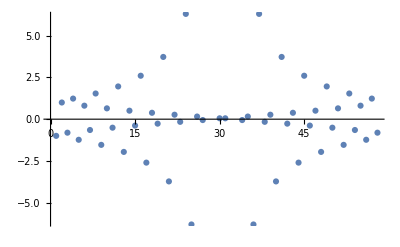

```mathematica
ListPlot[pl]
```

```mathematica
cf=Table[ContinuedFraction[N[pl[[i]],50]],{i,Length[pl]}]
```

ContinuedFraction::start: Warning: ContinuedFraction was unable to obtain at least one term using precision 50..

{ContinuedFraction[-1.],ContinuedFraction[1.],{0,-1,-4,-3,-1,-7,-1,-19,-1,-5,-1,-1,-1,-1,-1,-18,-5,-7,-1,-1,-3,-2,-1,-2,-33,-1,-1,-11,-18,-7,-2,-40,-5,-4,-1,-6,-3,-1,-46,-8,-1,-39,-3,-2},{1,4,3,1,7,1,19,1,5,1,1,1,1,1,18,5,7,1,1,3,2,1,2,33,1,1,11,18,7,2,40,5,4,1,6,3,1,46,8,1,39,3,2},{-1,-4,-3,-1,-7,-1,-19,-1,-5,-1,-1,-1,-1,-1,-18,-5,-7,-1,-1,-3,-2,-1,-2,-33,-1,-1,-11,-18,-7,-2,-40,-5,-4,-1,-6,-3,-1,-46,-8,-1,-39,-3,-2},{0,1,4,3,1,7,1,19,1,5,1,1,1,1,1,18,5,7,1,1,3,2,1,2,33,1,1,11,18,7,2,40,5,4,1,6,3,1,46,8,1,39,3,2},{0,-1,-1,-1,-5,-1,-3,-2,-1,-2,-2,-1,-3,-1,-10,-5,-1,-25,-1,-16,-1,-10,-3,-1,-4,-6,-2,-1,-1,-4,-1,-3,-1,-7,-1,-4,-17,-1,-15,-1,-3,-7,-3,-36,-3,-13,-1,-2,-1},{1,1,1,5,1,3,2,1,2,2,1,3,1,10,5,1,25,1,16,1,10,3,1,4,6,2,1,1,4,1,3,1,7,1,4,17,1,15,1,3,7,3,36,3,13,1,2,1},{-1,-1,-1,-5,-1,-3,-2,-1,-2,-2,-1,-3,-1,-10,-5,-1,-25,-1,-16,-1,-10,-3,-1,-4,-6,-2,-1,-1,-4,-1,-3,-1,-7,-1,-4,-17,-1,-15,-1,-3,-7,-3,-36,-3,-13,-1,-2,-1},{0,1,1,1,5,1,3,2,1,2,2,1,3,1,10,5,1,25,1,16,1,10,3,1,4,6,2,1,1,4,1,3,1,7,1,4,17,1,15,1,3,7,3,36,3,13,1,2,1},{0,-1,-1,-25,-1,-2,-1,-13,-12,-1,-1,-1,-1,-3,-7,-1,-5,-1,-2,-1,-3,-1,-25,-2,-133,-13,-8,-3,-3,-15,-77,-5,-3,-1,-2,-1,-2,-5,-10,-2,-1,-3,-3},{1,1,25,1,2,1,13,12,1,1,1,1,3,7,1,5,1,2,1,3,1,25,2,133,13,8,3,3,15,77,5,3,1,2,1,2,5,10,2,1,3,3},{-1,-1,-25,-1,-2,-1,-13,-12,-1,-1,-1,-1,-3,-7,-1,-5,-1,-2,-1,-3,-1,-25,-2,-133,-13,-8,-3,-3,-15,-77,-5,-3,-1,-2,-1,-2,-5,-10,-2,-1,-3,-3},{0,1,1,25,1,2,1,13,12,1,1,1,1,3,7,1,5,1,2,1,3,1,25,2,133,13,8,3,3,15,77,5,3,1,2,1,2,5,10,2,1,3,3},{0,-2,-1,-1,-1,-1,-7,-3,-1,-5,-1,-1,-41,-2,-3,-2,-240,-3,-4,-2,-8,-3,-1,-18,-8,-1142,-1,-1,-5,-2,-13,-3,-5,-5,-5,-1,-7,-1,-2,-1,-1},{2,1,1,1,1,7,3,1,5,1,1,41,2,3,2,240,3,4,2,8,3,1,18,8,1142,1,1,5,2,13,3,5,5,5,1,7,1,2,1,1},{-2,-1,-1,-1,-1,-7,-3,-1,-5,-1,-1,-41,-2,-3,-2,-240,-3,-4,-2,-8,-3,-1,-18,-8,-1142,-1,-1,-5,-2,-13,-3,-5,-5,-5,-1,-7,-1,-2,-1,-1},{0,2,1,1,1,1,7,3,1,5,1,1,41,2,3,2,240,3,4,2,8,3,1,18,8,1142,1,1,5,2,13,3,5,5,5,1,7,1,2,1,1},{0,-3,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2},{3,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2},{-3,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2},{0,3,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2},{0,-6,-3,-5,-2,-1,-14,-11,-2,-25,-1,-3,-1,-15,-1,-4,-3,-1,-1,-1,-2,-26,-1,-3,-4,-2,-2,-2,-5,-20,-3,-1,-3,-1,-11,-1,-8,-4,-8,-1,-2,-6,-2,-1,-1,-2,-2,-2,-1},{6,3,5,2,1,14,11,2,25,1,3,1,15,1,4,3,1,1,1,2,26,1,3,4,2,2,2,5,20,3,1,3,1,11,1,8,4,8,1,2,6,2,1,1,2,2,2,1},{-6,-3,-5,-2,-1,-14,-11,-2,-25,-1,-3,-1,-15,-1,-4,-3,-1,-1,-1,-2,-26,-1,-3,-4,-2,-2,-2,-5,-20,-3,-1,-3,-1,-11,-1,-8,-4,-8,-1,-2,-6,-2,-1,-1,-2,-2,-2,-1},{0,6,3,5,2,1,14,11,2,25,1,3,1,15,1,4,3,1,1,1,2,26,1,3,4,2,2,2,5,20,3,1,3,1,11,1,8,4,8,1,2,6,2,1,1,2,2,2,1},{0,-19,-12,-3,-12,-1,-4,-3,-5,-1,-34,-2,-2,-3,-1,-21,-1,-3,-1,-1,-6,-4,-4,-1,-2,-4,-1,-1,-3,-6,-2,-3,-1,-5,-1,-20,-1,-11,-23,-1,-3,-35,-4},{19,12,3,12,1,4,3,5,1,34,2,2,3,1,21,1,3,1,1,6,4,4,1,2,4,1,1,3,6,2,3,1,5,1,20,1,11,23,1,3,35,4},{-19,-12,-3,-12,-1,-4,-3,-5,-1,-34,-2,-2,-3,-1,-21,-1,-3,-1,-1,-6,-4,-4,-1,-2,-4,-1,-1,-3,-6,-2,-3,-1,-5,-1,-20,-1,-11,-23,-1,-3,-35,-4},{0,19,12,3,12,1,4,3,5,1,34,2,2,3,1,21,1,3,1,1,6,4,4,1,2,4,1,1,3,6,2,3,1,5,1,20,1,11,23,1,3,35,4},{0,19,12,3,12,1,4,3,5,1,34,2,2,3,1,21,1,3,1,1,6,4,4,1,2,4,1,1,3,6,2,3,1,5,1,20,1,11,23,1,3,35,4},{-19,-12,-3,-12,-1,-4,-3,-5,-1,-34,-2,-2,-3,-1,-21,-1,-3,-1,-1,-6,-4,-4,-1,-2,-4,-1,-1,-3,-6,-2,-3,-1,-5,-1,-20,-1,-11,-23,-1,-3,-35,-4},{19,12,3,12,1,4,3,5,1,34,2,2,3,1,21,1,3,1,1,6,4,4,1,2,4,1,1,3,6,2,3,1,5,1,20,1,11,23,1,3,35,4},{0,-19,-12,-3,-12,-1,-4,-3,-5,-1,-34,-2,-2,-3,-1,-21,-1,-3,-1,-1,-6,-4,-4,-1,-2,-4,-1,-1,-3,-6,-2,-3,-1,-5,-1,-20,-1,-11,-23,-1,-3,-35,-4},{0,6,3,5,2,1,14,11,2,25,1,3,1,15,1,4,3,1,1,1,2,26,1,3,4,2,2,2,5,20,3,1,3,1,11,1,8,4,8,1,2,6,2,1,1,2,2,2,1},{-6,-3,-5,-2,-1,-14,-11,-2,-25,-1,-3,-1,-15,-1,-4,-3,-1,-1,-1,-2,-26,-1,-3,-4,-2,-2,-2,-5,-20,-3,-1,-3,-1,-11,-1,-8,-4,-8,-1,-2,-6,-2,-1,-1,-2,-2,-2,-1},{6,3,5,2,1,14,11,2,25,1,3,1,15,1,4,3,1,1,1,2,26,1,3,4,2,2,2,5,20,3,1,3,1,11,1,8,4,8,1,2,6,2,1,1,2,2,2,1},{0,-6,-3,-5,-2,-1,-14,-11,-2,-25,-1,-3,-1,-15,-1,-4,-3,-1,-1,-1,-2,-26,-1,-3,-4,-2,-2,-2,-5,-20,-3,-1,-3,-1,-11,-1,-8,-4,-8,-1,-2,-6,-2,-1,-1,-2,-2,-2,-1},{0,3,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2},{-3,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2},{3,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2},{0,-3,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2,-1,-2},{0,2,1,1,1,1,7,3,1,5,1,1,41,2,3,2,240,3,4,2,8,3,1,18,8,1142,1,1,5,2,13,3,5,5,5,1,7,1,2,1,1},{-2,-1,-1,-1,-1,-7,-3,-1,-5,-1,-1,-41,-2,-3,-2,-240,-3,-4,-2,-8,-3,-1,-18,-8,-1142,-1,-1,-5,-2,-13,-3,-5,-5,-5,-1,-7,-1,-2,-1,-1},{2,1,1,1,1,7,3,1,5,1,1,41,2,3,2,240,3,4,2,8,3,1,18,8,1142,1,1,5,2,13,3,5,5,5,1,7,1,2,1,1},{0,-2,-1,-1,-1,-1,-7,-3,-1,-5,-1,-1,-41,-2,-3,-2,-240,-3,-4,-2,-8,-3,-1,-18,-8,-1142,-1,-1,-5,-2,-13,-3,-5,-5,-5,-1,-7,-1,-2,-1,-1},{0,1,1,25,1,2,1,13,12,1,1,1,1,3,7,1,5,1,2,1,3,1,25,2,133,13,8,3,3,15,77,5,3,1,2,1,2,5,10,2,1,3,3},{-1,-1,-25,-1,-2,-1,-13,-12,-1,-1,-1,-1,-3,-7,-1,-5,-1,-2,-1,-3,-1,-25,-2,-133,-13,-8,-3,-3,-15,-77,-5,-3,-1,-2,-1,-2,-5,-10,-2,-1,-3,-3},{1,1,25,1,2,1,13,12,1,1,1,1,3,7,1,5,1,2,1,3,1,25,2,133,13,8,3,3,15,77,5,3,1,2,1,2,5,10,2,1,3,3},{0,-1,-1,-25,-1,-2,-1,-13,-12,-1,-1,-1,-1,-3,-7,-1,-5,-1,-2,-1,-3,-1,-25,-2,-133,-13,-8,-3,-3,-15,-77,-5,-3,-1,-2,-1,-2,-5,-10,-2,-1,-3,-3},{0,1,1,1,5,1,3,2,1,2,2,1,3,1,10,5,1,25,1,16,1,10,3,1,4,6,2,1,1,4,1,3,1,7,1,4,17,1,15,1,3,7,3,36,3,13,1,2,1},{-1,-1,-1,-5,-1,-3,-2,-1,-2,-2,-1,-3,-1,-10,-5,-1,-25,-1,-16,-1,-10,-3,-1,-4,-6,-2,-1,-1,-4,-1,-3,-1,-7,-1,-4,-17,-1,-15,-1,-3,-7,-3,-36,-3,-13,-1,-2,-1},{1,1,1,5,1,3,2,1,2,2,1,3,1,10,5,1,25,1,16,1,10,3,1,4,6,2,1,1,4,1,3,1,7,1,4,17,1,15,1,3,7,3,36,3,13,1,2,1},{0,-1,-1,-1,-5,-1,-3,-2,-1,-2,-2,-1,-3,-1,-10,-5,-1,-25,-1,-16,-1,-10,-3,-1,-4,-6,-2,-1,-1,-4,-1,-3,-1,-7,-1,-4,-17,-1,-15,-1,-3,-7,-3,-36,-3,-13,-1,-2,-1},{0,1,4,3,1,7,1,19,1,5,1,1,1,1,1,18,5,7,1,1,3,2,1,2,33,1,1,11,18,7,2,40,5,4,1,6,3,1,46,8,1,39,3,2},{-1,-4,-3,-1,-7,-1,-19,-1,-5,-1,-1,-1,-1,-1,-18,-5,-7,-1,-1,-3,-2,-1,-2,-33,-1,-1,-11,-18,-7,-2,-40,-5,-4,-1,-6,-3,-1,-46,-8,-1,-39,-3,-2},{1,4,3,1,7,1,19,1,5,1,1,1,1,1,18,5,7,1,1,3,2,1,2,33,1,1,11,18,7,2,40,5,4,1,6,3,1,46,8,1,39,3,2},{0,-1,-4,-3,-1,-7,-1,-19,-1,-5,-1,-1,-1,-1,-1,-18,-5,-7,-1,-1,-3,-2,-1,-2,-33,-1,-1,-11,-18,-7,-2,-40,-5,-4,-1,-6,-3,-1,-46,-8,-1,-39,-3,-2}}

```mathematica
w=Union[Table[FromContinuedFraction[cf[[i]]],{i,3,Length[cf]}]]
```

{-2956681819797243042162764/154953128222114520398013,-4182409487901499458481486/662428585949309441412027,-11550219564299987974035401/3094872004656335742165753,-1466223401133814357779589/562830431022577023141325,-2728608570512946986632541/1390295508384960163553365,-474578856978845935775277/308195113293057934935035,-6908055001890171227925647/5594032640963565584411468,-5594032640963565584411468/6908055001890171227925647,-308195113293057934935035/474578856978845935775277,-1390295508384960163553365/2728608570512946986632541,-562830431022577023141325/1466223401133814357779589,-3094872004656335742165753/11550219564299987974035401,-662428585949309441412027/4182409487901499458481486,-154953128222114520398013/2956681819797243042162764,154953128222114520398013/2956681819797243042162764,662428585949309441412027/4182409487901499458481486,3094872004656335742165753/11550219564299987974035401,562830431022577023141325/1466223401133814357779589,1390295508384960163553365/2728608570512946986632541,308195113293057934935035/474578856978845935775277,5594032640963565584411468/6908055001890171227925647,6908055001890171227925647/5594032640963565584411468,474578856978845935775277/308195113293057934935035,2728608570512946986632541/1390295508384960163553365,1466223401133814357779589/562830431022577023141325,11550219564299987974035401/3094872004656335742165753,4182409487901499458481486/662428585949309441412027,2956681819797243042162764/154953128222114520398013}

```mathematica
N[w]
```

```mathematica
f1[z_,i_]:=N[-Exp[2*π*I*w[[i]]]*z^2*(z−4)/(1−4z),100]
```

```mathematica
g1=Flatten[ParallelTable[{JuliaSetPlot[f1[z,i],z,ImageSize->{940,560},PlotRange->{{-4.05,7.55},{-5.8,5.8}},ColorFunction->Hue],JuliaSetPlot[f1[z,i],z,ImageSize->{940,560},PlotRange->{{-4.05,7.55},{-5.8,5.8}},ColorFunction->Hue],JuliaSetPlot[f1[z,i],z,ImageSize->{940,560},PlotRange->{{-4.05,7.55},{-5.8,5.8}},ColorFunction->Hue]},{i,Length[w]}]];
```

SubKernels`SubKernels::timekernels: Timeout for subkernels. Received only 0 of 4 connections.

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
Export["Herman_rings_movie3x_Fuchsian.10_235neg30_Hue.mp4",g1]
```

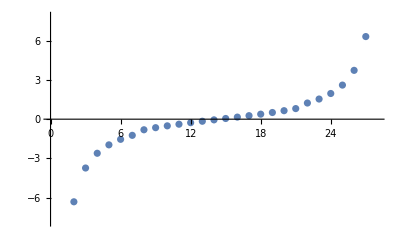

```mathematica
ListPlot[w]
```

```mathematica
cfl=Table[Length[cf[[i]]],{i,3,Length[cf]}]
```

{44,43,43,44,49,48,48,49,43,42,42,43,41,40,40,41,88,87,87,88,49,48,48,49,43,42,42,43,43,42,42,43,49,48,48,49,88,87,87,88,41,40,40,41,43,42,42,43,49,48,48,49,44,43,43,44}

```mathematica
max=Max[cfl]
```

88

```mathematica
Union[Table[If[Length[cf[[i]]]==max,FromContinuedFraction[cf[[i]]],Nothing],{i,Length[cf]}]]
```

{-3094872004656335742165753/11550219564299987974035401,3094872004656335742165753/11550219564299987974035401}

```mathematica
N[%]
```

{-0.267949,0.267949}

```mathematica
cfm=Table[Max[cf[[i]]],{i,Length[cf]}]
```

{ContinuedFraction[-1.],ContinuedFraction[1.],0,46,-1,46,0,36,-1,36,0,133,-1,133,0,1142,-1,1142,0,3,-1,3,0,26,-1,26,0,35,-1,35,35,-1,35,0,26,-1,26,0,3,-1,3,0,1142,-1,1142,0,133,-1,133,0,36,-1,36,0,46,-1,46,0}

```mathematica
maxm=Max[cfm][[1]]
```

1142

```mathematica
Union[Table[If[Max[cf[[i]]]==maxm,FromContinuedFraction[cf[[i]]],Nothing],{i,Length[cf]}]]

N[%]
```

{562830431022577023141325/1466223401133814357779589,1466223401133814357779589/562830431022577023141325,If[ContinuedFraction[-1.]==1142,FromContinuedFraction[cf⟦i⟧],Nothing],If[ContinuedFraction[1.]==1142,FromContinuedFraction[cf⟦i⟧],Nothing]}

ContinuedFraction::start: Warning: ContinuedFraction was unable to obtain at least one term using precision 15.9546.

{0.383864,2.60509,If[ContinuedFraction[-1.]==1142.,FromContinuedFraction[cf⟦i⟧],Nothing],If[ContinuedFraction[1.]==1142.,FromContinuedFraction[cf⟦i⟧],Nothing]}